```mathematica
ClearAll[odeSolver];

Options[odeSolver]={"Method"->"Euler"};

odeSolver[f_,X0_List,tf_?NumericQ,n_Integer?Positive,OptionsPattern[]]:=Module[{h,datalist,prev,next,r1,r2,r3,r4,method},(*step size*)h=N[(tf-X0[[1]])/n];
(*normalize/tolerate various method names*)method=ToLowerCase@ToString@OptionValue["Method"];
For[datalist={X0},(*start*)Length[datalist]<=n,(*test*)AppendTo[datalist,next],(*incr*)(*body*)prev=Last[datalist];
Switch[method,"euler",next=prev+h (f@prev),"rk2"|"heun"|"improvedeuler",r1=f@prev;
r2=f@(prev+h r1);
next=prev+(h/2) (r1+r2),"rk4",r1=f@prev;
r2=f@(prev+(h/2) r1);
r3=f@(prev+(h/2) r2);
r4=f@(prev+h r3);
next=prev+(h/6) (r1+2 r2+2 r3+r4),_,(*default to Euler if unrecognized*)next=prev+h (f@prev)];];
datalist]
```

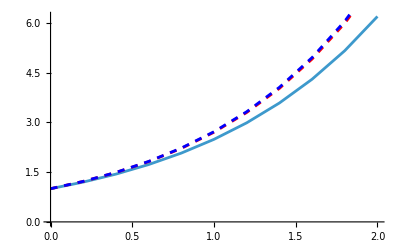

```mathematica
F[{t_,y_}]:={1,y};                 (*dt/ds=1,dy/ds=y*)
Show[ListPlot[odeSolver[F,{0,1},2,10,"Method"->"Euler"],Joined->True],ListPlot[odeSolver[F,{0,1},2,10,"Method"->"rk2"],PlotStyle->{Red,Dashed},Joined->True],ListPlot[odeSolver[F,{0,1},2,10,"Method"->"rk4"],PlotStyle->{Blue,Dashed},Joined->True]]
```

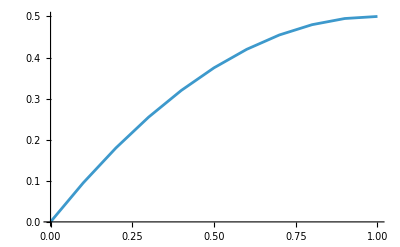

```mathematica
ClearAll[F];
F[{t_,x_}]={1,1-t};
ListPlot[odeSolver[F,{0,0},1,10,"Method"-> "rk4"],Joined->True]
```

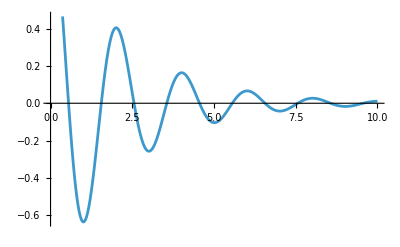

```mathematica
f2[{t_,c_,i_}]={1,i,-10 c-i };
X0={0,1,0};
ListPlot[odeSolver[f2,X0,10,1000,"Method"-> "Euler"][[;;,{1,2}]],Joined->True]
```

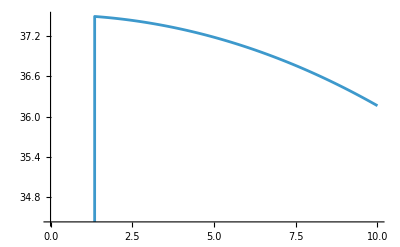

```mathematica
f3[{t_,x_}]={1,-t/x};
ListPlot[odeSolver[f3,{0,1},10,1000,"Method"->"Euler"],Joined->True]
```